```mathematica
<<D:\\Economics\Courses\MGSC533\2021\Math\EqPrice.m
```

```mathematica
(*  UTILITY FUNCTIONS       *)
```

```mathematica
U[x1_, x2_, c_]:= If[x1 * x2 > 0, 
                              c[[4]] * ((c[[1]] * x1)^c[[3]] 
                                          + (c[[2]] * x2)^c[[3]])^(1/c[[3]]),
                              0]
```

```mathematica
cA = {0.362, 109.89, -1, 0.695}
```

{0.362,109.89,-1,0.695}

```mathematica
cB = {2.982, 109.89, -1, 0.256}
```

{2.982,109.89,-1,0.256}

```mathematica
(*  DEMAND FOR GOOD Y FOR THE BUYER AND FOR THE SELLER                   *)
(*  Parameters are: price (p), endowment (x0, y0), utility weights 'a'   *)
(*  and 'b' on allocation x and y, multiplicative coefficient α on       *)
(*  Firm 1 production, exponent γ on Firm 1 production, multiplicative   *)
(*  coefficient β on Firm 2 production, income share of Buyer on Firm 1  *)
(*  profit.                                                              *)
```

```mathematica
yB[p_,x0_,y0_,a_,b_,r_,α_, γ_, β_,sB_]:=(p[[1]] * x0 + p[[2]] * y0 + sB/2 * (α * γ * p[[2]])^(1/(1 - γ)) * p[[1]]^(-γ/(1 - γ)) * (1/γ - 1)+(1/4) * (β * p[[1]])^2/(4 * p[[2]])) * p[[2]]^(1/(r-1)) *a^(r/(r - 1))/((b * p[[1]])^(r/(r - 1))+(a * p[[2]])^(r/(r - 1)))
```

```mathematica
yS[p_,x0_,y0_,a_,b_,r_,α_,γ_, β_,sB_]:=(p[[1]] * x0 + p[[2]] * y0 + (1 - sB)/2 * (α * γ * p[[2]])^(1/(1 - γ))*(1/γ - 1)*p[[1]]^(-γ/(1 - γ))+(1/4) * (β * p[[1]])^2/(4 * p[[2]])) * p[[2]]^(1/(r - 1))*a^(r/(r - 1))/((b * p[[1]])^(r/(r - 1)) + (a * p[[2]])^(r/(r - 1)))
```

```mathematica
(*  DEMAND FOR GOOD X FOR THE BUYER AND FOR THE SELLER                   *)
(*  Parameters are the same as the parameters for commodity Y.           *)
```

```mathematica
xB[p_, x0_, y0_, a_, b_, r_, α_,γ_, β_, sB_]:= (p[[1]] * x0 + p[[2]] * y0 + sB/2 * (α * γ * p[[2]])^(1/(1 - γ)) * p[[1]]^(-γ/(1 - γ)) * (1/γ - 1)+(1/4) * (β * p[[1]])^2/(4 * p[[2]])) * p[[1]]^(1/(r-1)) *b^(r/(r - 1))/((b * p[[1]])^(r/(r - 1))+(a * p[[2]])^(r/(r - 1)))
```

```mathematica
xS[p_, x0_, y0_, a_, b_, r_, α_,γ_, β_, sB_]:= (p[[1]] * x0 + p[[2]] * y0 + (1 - sB)/2 *(α * γ * p[[2]])^(1/(1 - γ))*(1/γ - 1)*p[[1]]^(-γ/(1 - γ))+(1/4) * (β * p[[1]])^2/(4 * p[[2]])) * p[[1]]^(1/(r - 1))*b^(r/(r - 1))/((b * p[[1]])^(r/(r - 1)) + (a * p[[2]])^(r/(r - 1)))
```

```mathematica
(*  Find the demand for each agent when there is no production.    *)
```

```mathematica
{yB[{1, 90.94056},1800, 0, 0.362, 109.89, -1, 0, 0.5, 0, 0], yS[{1, 90.94056}, 0, 18, 2.982, 109.89,  -1, 0, 0.5, 0, 0]}
```

{7.00139,10.9986}

```mathematica
{xB[{1, 90.94056},1800, 0, 0.362, 109.89, -1, 0, 0.5, 0, 0], xS[{1, 90.94056}, 0, 18, 2.982, 109.89,  -1, 0, 0.5, 0, 0]}
```

{1163.29,636.71}

```mathematica
(*  Form the excess demand for commodity Y when there are 6 buyers,      *)
(*  6 sellers, and 3 firms of each type.                                 *)
```

```mathematica
ZY[α_, γ_, β_, sB_, p_]:=6 * yB[p, 1800, 0, 0.362, 109.89, -1, α, γ, β, sB]+6 * (yS[p, 0, 18, 2.982, 109.89, -1, α, γ, β, sB] - 18) - 3 * α^(1/(1 - γ)) * (γ * p[[2]]/p[[1]])^(γ/(1 - γ)) + 3 * (β  *  p[[1]])^2/(4 * p[[2]]^2)
```

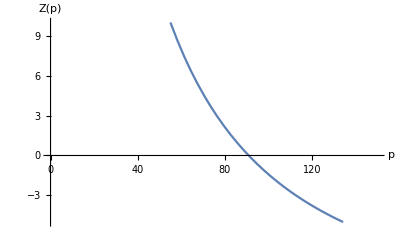

```mathematica
Plot[ZY[0, 0.5, 0, 0, {1, p}], {p, 0.01, 150}, PlotRange -> {{0, 150.04}, {-5, 10}}, AxesLabel-> {"p", "Z(p)"},LabelStyle->{FontSize->11,Black}]
```

```mathematica
ZY[0, 0.5, 0, 0, {1, 90.940560244}]
```

1.36431×10^-10

```mathematica
(*  Find the excess demands for good Y by each agent and each firm.       *)
(*  The output of Y[p, α, γ, β, sB] is a vector with the excess demand   *)
(*  of the 6 buyers.  The excess demand of the 6 sellers.  The demand     *)
(*  for commodity Y by the three firms of type Firm 1 (which is negative  *)
(*  because these firms produce commodity Y) and the demand for           *)
(*  commodity Y by the three firms of type Firm 2.                        *)
```

```mathematica
Y[p_, α_, γ_, β_, sB_]:= {yB[p,1800, 0, 0.362, 109.89, -1,α,γ, β, sB], (yS[p,0, 18, 2.982, 109.89, -1, α,γ, β, sB] - 18), -α^(1/(1 - γ)) * (γ * p[[2]]/p[[1]])^(γ/(1 - γ)),(β  *  p[[1]])^2/(4 * p[[2]]^2)}
```

```mathematica
Y[{1, 90.94056}, 0, 0.5, 0, 0]
```

{7.00139,-7.00139,0.,0.}

```mathematica
(*  Find the excess demands for good X by each agent and each firm.      *)
(*  The output of X[p, α, γ, β, sB] is similar to the output of         *)
(*  Y[p, α, γ, β, sB].                                                  *)
```

```mathematica
X[p_, α_, γ_, β_, sB_]:= {xB[p,1800, 0, 0.362, 109.89, -1,α, γ, β, sB] - 1800, xS[p,0, 18, 2.982, 109.89, -1, α, γ, β, sB], (α * γ * p[[2]]/p[[1]])^(1/(1 - γ)), - β^2 * p[[1]]/(2 * p[[2]])}
```

```mathematica
X[{1, 90.94056}, 0, 0.5, 0, 0]
```

{-636.71,636.71,0.,0.}

```mathematica
(*  THE CHALLENGE NOW IS TO FIND A PRODUCTION FUNCTION FOR FIRM 1 THAT   *)
(*  RESULTS IN INTEGER LEVELS OF THE INPUTS TO EACH FIRM OF TYPE FIRM 1  *)
(*  AS WELL AS INTEGER OUTPUT FOR FIRM 1, AN INTEGER PRICE, AND INTEGER  *) (*  DEMAND LEVELS FOR X AND Y FOR THE BUYERS AND FOR THE SELLERS.        *)
```

```mathematica
(*  The first step is to calculate the equilibrium price.     *)
```

```mathematica
yB[{1, 28.99}, 1800, 0, 0.362, 109.89, -1, 0.55177, 0.58, 0, 0.54326]
```

14.9801

```mathematica
yB[{1/29.99, 28.99/29.99}, 1800, 0, 0.362, 109.89, -1, 0.55177, 0.58, 0, 0.54326]
```

14.9801

```mathematica
yS[{1/29.99, 28.99/29.99}, 0, 18, 2.982, 109.89, -1,0.55177, 0.58, 0, 0.54326]
```

9.00001

```mathematica
ZY[0.55177, 0.58, 0, 0.54326, {1, 28.99}]
```

0.0000806348

```mathematica
ZY[0.55177, 0.58, 0, 0.54326, {1/29.99, 28.99/29.99}]
```

0.0000806348

```mathematica
EqPrice[0.55177, 0.58, 0, 0.54326,  10000]
```

28.99

```mathematica
(*  The next step is to evaluate the demands for Y for agents and firms  *)
(*  at the equilibrium price to see if any of them are integers.         *)
```

```mathematica
YatEqPrice[α_, γ_, sB_]:= {EqPrice[α, γ, 0, sB, 10000], Y[{1, EqPrice[α, γ, 0, sB, 10000]}, α, γ, 0, sB]}
```

```mathematica
YatEqPrice[0.55177, 0.58, 0.54326]
```

{28.99,{14.9801,-8.99999,-11.9602,0.}}

```mathematica
XatEqPrice[α_, γ_, sB_]:= {EqPrice[α, γ, 0, sB, 10000], X[{1, EqPrice[α, γ, 0, 0.5, 10000]}, α, γ, 0, sB]}
```

```mathematica
XatEqPrice[0.55177, 0.58, 0.54326]
```

{28.99,{-394.893,294.633,202.,0.}}

```mathematica
(*  We can look at a numnber of values of the parameters to see if any   *)
(*  of them lead to integer values for the equilibrium price as well     *)
(*  integer values of the output of Y by the firms.                      *)
```

```mathematica
IntegerPriceOutput[α_, γ_, sB_]:= Module[{py, pInt, yInt, yB, yS, x, xIn},
py = YatEqPrice[α, γ, sB];
x = XatEqPrice[α, γ, sB];
pInt = Abs[py[[1]] - Round[py[[1]]]];
yInt = Abs[py[[2, 3]] - Round[py[[2, 3]]]];
yB =  Abs[py[[2, 1]] - Round[py[[2, 1]]]];
yS =  Abs[py[[2, 2]] - Round[py[[2, 2]]]];
xIn = Abs[x[[2, 3]] - Round[x[[2, 3]]]];
Return[pInt + yInt + yB+ yS + xIn ]]
```

```mathematica
(*  The parameters in the next function give near integer values for price,  *)
(*  Firm 1 output and yB.                                                    *)
```

```mathematica
ParallelTable[Table[Table[IntegerPriceOutput[0.55177+ 0.00001 * i, 0.58 + 0.00001 * j, 0.54326+ 0.00001 * k], {k, -2, 2}], {j, -2,2}], {i, -2,2}];
```

```mathematica
{ Min[%], Position[%, Min[%]]}
```

{0.0701991,{{3,3,3}}}

```mathematica
ZY[α_, γ_, sB_,p_]:=6 * ((1800 + sB/2 * (α * γ * p)^(1/0.42) * (21/29)) * p^(-0.5) * 0.362^0.5)/(109.89^0.5 + (0.362 * p)^0.5) + 6 * ((18 * p + (1 - sB)/2 * (α * γ * p)^(1/0.42) * (21/29)) * p^(-0.5) * 2.982^0.5)/(109.89^0.5 + (2.982 * p)^0.5) - 108 - 3 * α^(1/0.42) * (0.58 * p)^(29/21)
```

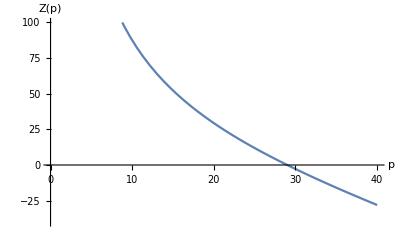

```mathematica
Plot[ZY[0.55177, 0.58, 0.54326, p], {p, 0.01, 40}, PlotRange -> {{0, 40.04}, {-40, 100}}, AxesLabel-> {"p", "Z(p)"},LabelStyle->{FontSize->11,Black}]
```

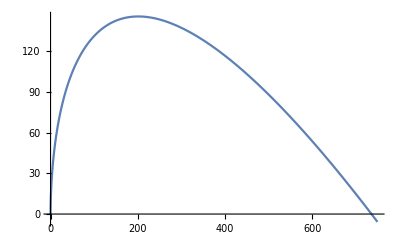

```mathematica
Plot[29*0.55177*(x^0.58)-x,{x,0,750}]
```